```mathematica
I1=Image[GeoGraphics[GeoRange->"World",ImageSize->600]]
```

-Graphics-

```mathematica
ImageTransformation[I1,Sqrt]
```

-Graphics-

```mathematica
r0=Disk[{1,1},4];
f={Indexed[#,1] Indexed[#,2],Indexed[#,1]+Indexed[#,2]}&;
p={-2,2};
r1=Transform[r0,f];
```

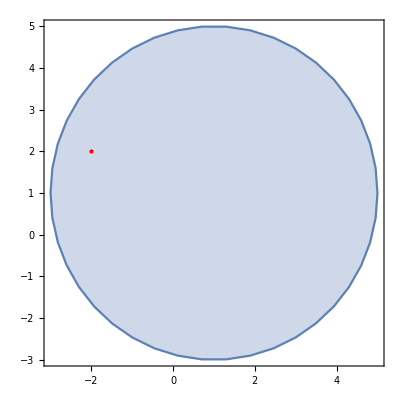

```mathematica
RegionPlot[r0,Epilog->{Red,Point[p]}]
```

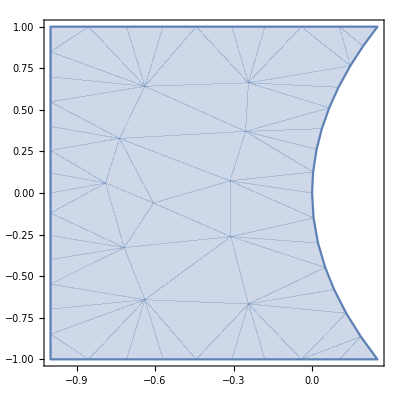

```mathematica
RegionPlot[r1,Epilog->{Red,Point[f[p]]}]
```

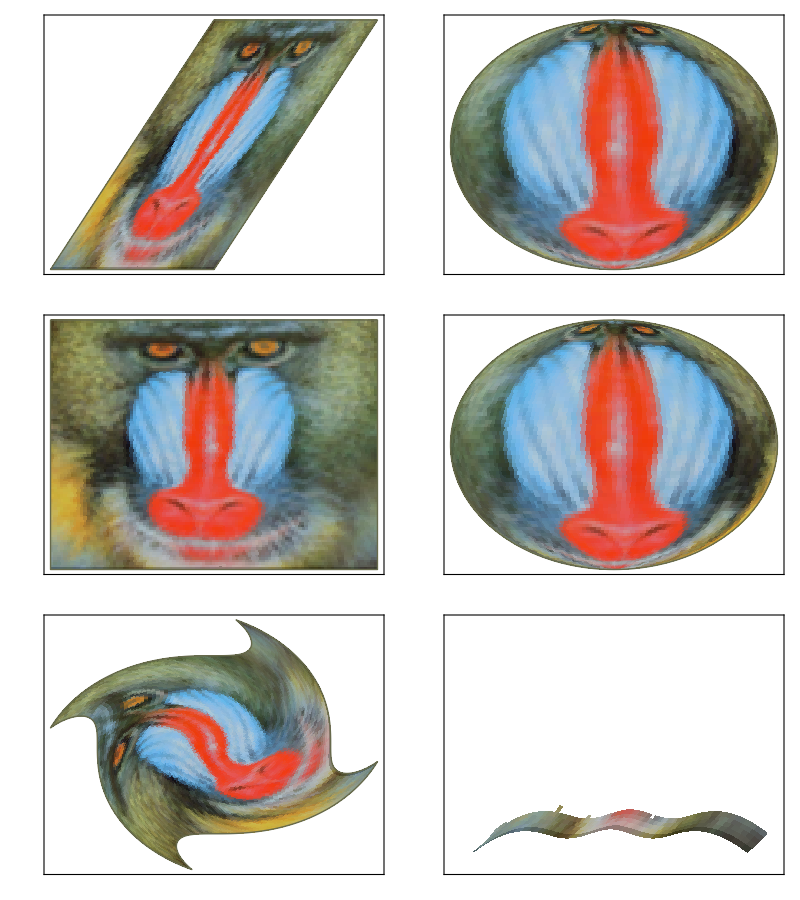

```mathematica
img=ImageResize[-Graphics-,250];

col=BSplineFunction[ImageData[img]];
f=BSplineFunction[Table[{i+.5(-1)^j,j+.5(-1)^i},{i,7},{j,7}]];
opts={PlotPoints->100,MaxRecursion->0,Mesh->None,ColorFunction->(col[1-#4,#3]&),Axes->None,FrameTicks->None};
Grid[{{ParametricPlot[{ u+v,v},{u,-1,1},{v,-1,1},Evaluate[opts]],ParametricPlot[{Cos[t]Cos[s],Sin[s]},{t,0,Pi},{s,-Pi/2,Pi/2},Evaluate[opts]]},
{ParametricPlot[{u,v},{u,0,1},{v,0,1},Evaluate[opts]],ParametricPlot[{Cos[t]Cos[s],Sin[s]},{t,0,Pi},{s,-Pi/2,Pi/2},Evaluate[opts]]},{ParametricPlot[Evaluate[{u Cos[d]-v Sin[d],v Cos[d]+u Sin[d]}/.d->Pi/2 Norm[{u,v}]],{u,-1,1},{v,-1,1},Evaluate[opts]],ParametricPlot[f[u,v],{u,0,1},{v,0,1},Evaluate[opts]]}}]
```

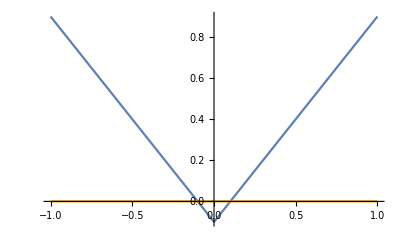

```mathematica
Plot[{Abs[x]-0.1,0},{x,-1,1}]
```